```mathematica
ϵ = 1.*8065.5;
α = 10/3.14;
ω0 = 300;
wc = 53;
Γ = N[ω0^2/wc];
Temp = 300;
kB = 0.695;
```

```mathematica
ρ00i = 0.5;
ρ01i = 0.5;
ρ10i = 0.5;
ρ11i= 0.5;
```

```mathematica
β = 1/(kB Temp)
```

0.00479616

```mathematica
J[ω_]:= α Γ ω0 ω /((ω0^2 - ω^2)^2 + Γ^2 ω^2)
```

```mathematica
S1:= -4 NIntegrate[J[ω] Coth[ω/(2 kB Temp)], {ω, 0, 10 wc},MaxRecursion->50]
S2[t_]:=-4 NIntegrate[J[ω] Coth[ω/(2 kB Temp)] Cos[ω t], {ω, 0, 10 wc},MaxRecursion->50]
```

```mathematica
rho01[t_] := ρ10i Exp[S1-S2[t]] Exp[ⅈ ϵ t]
```

```mathematica
rho01[t_] := ρ01i Exp[S1-S2[t]] Exp[-ⅈ ϵ t]
```

```mathematica
t0 = 0; tf= 0.01; di =(tf-t0)/2000;
tlist = N[Range[t0,tf, di]];
```

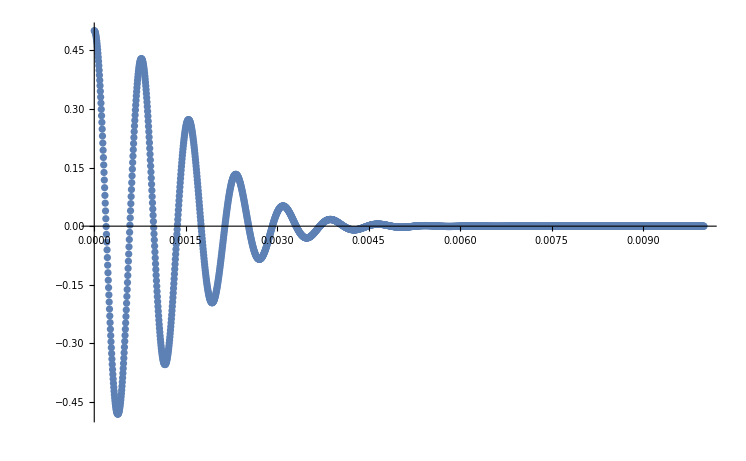

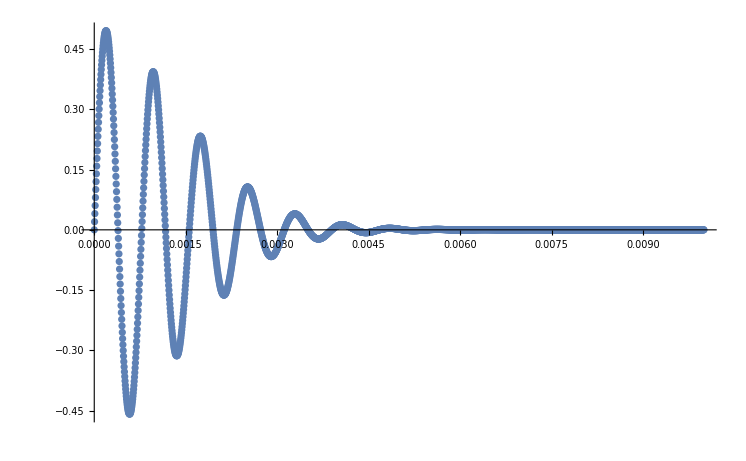

```mathematica
ListPlot[Transpose@{tlist, Re@rho01[tlist]}, PlotRange->All]
ListPlot[Transpose@{tlist, Im@rho01[tlist]}, PlotRange->All]
```